## Basic CR model

### Initialize constants

Set number of consumers, resources, and enzyme budget

```mathematica
m=5;
p=3;
enzymeBudget=1;
```

Define constants for each consumer

```mathematica
c=enzymeBudget*Normalize[#,Total]&/@RandomReal[{0,1},{m,p}](*preference vector for each species*)
```

{{0.520954,0.188771,0.290275},{0.440663,0.394514,0.164823},{0.356436,0.36332,0.280244},{0.608024,0.351345,0.0406306},{0.185041,0.723137,0.0918212}}

```mathematica
g=Table[1,m,p](*metabolic conversion coefficient for each resource*)
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

```mathematica
z=Table[0.1,m](*loss function/death for each species*)
```

{0.1,0.1,0.1,0.1,0.1}

Define constants for each resource

```mathematica
κ=Table[0.3,p]
```

{0.3,0.3,0.3}

```mathematica
μ=Table[0,p]
```

{0,0,0}

### Initialize populations

```mathematica
r0=Table[1,p]
```

{1,1,1}

```mathematica
n0=Table[1,m]
```

{1,1,1,1,1}

### Solve The differential equations

```mathematica
sols=NDSolve[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
{r,n},
{t,0,10000}][[1]];
```

### Plot dynamics

```mathematica
sols
```

{r→InterpolatingFunction[…],n→InterpolatingFunction[…]}

```mathematica
Show[Plot3D[1-x-y,{x,0,1},{y,0,1},PlotStyle->Directive[Opacity[0.3]]],ListPointPlot3D[List/@c],AspectRatio->1]
```

-Graphics3D-

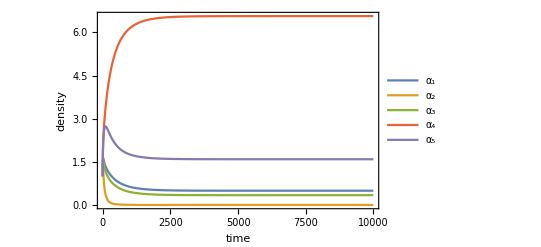

```mathematica
Plot[Evaluate[Table[Indexed[n[t],a]/.sols,{a,m}]],{t,0,10000},PlotRange->{All,{0,All}},Frame->True,FrameLabel->{"time","density"},PlotLegends->{"α_1","α_2","α_3","α_4","α_5"}]
```

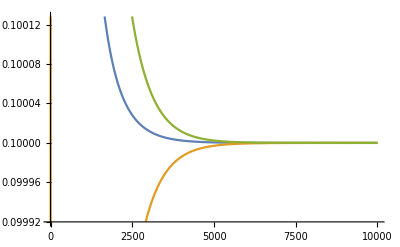

```mathematica
Plot[Evaluate[Table[Indexed[r[t],j]/.sols,{j,p}]],{t,0,10000}]
```

### Equilibrium state

```mathematica
crSteadyState[{n0_,c_,g_,z_},r0_,κ_,μ_,tMax_:10000]:=
NDSolveValue[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
n,
{t,0,tMax}][tMax]
```

```mathematica
crSteadyState[{n0,c,g,z},r0,κ,μ,10000]
```

{0.344008,1.70589×10^-13,8.65599,-3.84148×10^-22,-4.858×10^-15}

## HGT

Mutate one of the vectors and change all the corresponding vectors

```mathematica
(*Input: each of the variables involving α 
Output: each of the updated variables*)
```

```mathematica
{4,2,3}*{1,1,3}
```

{4,2,9}

```mathematica
mutate[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0,p=Length[c[[1]]],mutation},
		mutation=Table[RandomVariate[UniformDistribution[{1,1.03}]],p];
		AppendTo[c,enzymeBudget*Normalize[Ramp[RandomChoice[Ramp[n]->c]*mutation],Total]];
		AppendTo[n,2];
		AppendTo[g,Table[1,p]];
		AppendTo[z,0.1];
		{n,c,g,z}
	]
```

```mathematica
mutate[{n0,c,g,z}]
```

{{1,1,1,1,1,2},{{0.491571,0.403744,0.104685},{0.153196,0.797863,0.0489411},{0.511719,0.419206,0.0690746},{0.370881,0.291886,0.337233},{0.0909375,0.462768,0.446295},{0.492686,0.404685,0.102628}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1}}

h_{ij} = n_in_j/n_T^2, where the total abundance in the community is n_T, and n_i, n_

```mathematica
mutateHGTOneStep[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0,p=Length[c[[1]]],mutation,h},
	(*mutation*)
		mutation=Table[RandomVariate[UniformDistribution[{1,1.03}]],p];
		AppendTo[c,enzymeBudget*Normalize[Ramp[RandomChoice[Ramp[n]->c]*mutation],Total]];
		AppendTo[n,0.1];
		AppendTo[g,Table[1,p]];
		AppendTo[z,0.1];
		n=Chop[crSteadyState[{n,c,g,z},r0,κ,μ]];
		(*create h, probability of gene transfer from the newly mutated individual
		(works because it's always last index)*)
		h=Append[Table[(n[[i]]*n[[-1]])/Total[n],{i,1,(Length[n]-1)}],0];
		(*horizontal gene transfer*)
		Do[
			If[RandomReal[]<h[[i]],
				c[[i]] = Normalize[Ramp[c[[i]]*mutation],Total]
			],
			{i,Length[n]}
		];
		n=Ramp[Chop[crSteadyState[{n,c,g,z},r0,κ,μ]]];
		{n,c,g,z}
	]
```

```mathematica
mutateHGTOneStep[{n0,c,g,z}]
```

{{0.341826,0,8.65817,0,0,0},{{0.520954,0.188771,0.290275},{0.440663,0.394514,0.164823},{0.356436,0.36332,0.280244},{0.608024,0.351345,0.0406306},{0.185041,0.723137,0.0918212},{0.613188,0.346873,0.0399391}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1}}

```mathematica
runHGT=NestList[mutateHGTOneStep,{n0,c,g,z},100];
```

```mathematica
runHGT[[All,1]]
```

```mathematica
bugState={{-2.153373452191634*^40,-1.3585266659002686*^43,4.818162725961764*^36,1.8808976291505273*^48,1.4548699592826546*^41,-3.3507986200882615*^46,2.953990493866936*^33,0,-1.1510106195825386*^38,0,0,0,0,0,0,0,0,0,0,3.2165873380279263*^40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.766343506716481*^23,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.038931597016594*^24,0,0,0,-1.6646988805643444*^45,-9.689117063392348*^41,-1.5058933008405675*^45},{{0.5209537510080495,0.18877123036426002,0.29027501862769045},{0.4406625778464477,0.3945143920395882,0.16482303011396413},{0.3524736026882815,0.3654839220382609,0.2820424752734575},{0.6080243168086128,0.35134510593384044,0.04063057725754676},{0.18504133408656218,0.7231374755118568,0.09182119040158097},{0.4818064130791882,0.18647787598778687,0.3317157109330247},{0.35037593132201716,0.3635238848338055,0.28610018384417735},{0.3519042338956315,0.3620690948121281,0.2860266712922406},{0.3471592952590099,0.3644575330932129,0.2883831716477773},{0.3483280926460153,0.36583691219901454,0.28583499515497024},{0.34944837642421434,0.36668151006556127,0.2838701135102245},{0.34732567196458136,0.3643604167857851,0.28831391124963357},{0.34521699513665793,0.3666538270971838,0.2881291777661582},{0.3503044168005793,0.36564594908599385,0.28404963411342693},{0.3456522606503919,0.36794014298966715,0.2864075963599411},{0.3482883944510473,0.3599581697922336,0.29175343575671914},{0.5116900721297428,0.19353924818648738,0.29477067968376985},{0.34985295207191147,0.35997328595247946,0.29017376197560896},{0.35097941999479193,0.3575517436601163,0.2914688363450918},{0.35126846464501,0.35928462165412317,0.28944691370086695},{0.3484200641221626,0.3595199950795072,0.2920599407983302},{0.35347523300506434,0.3549457430223158,0.29157902397261987},{0.3500895156709365,0.359031506827776,0.29087897750128744},{0.5146456036234708,0.19031717309932142,0.2950372232772079},{0.34896922815581594,0.35911437706736393,0.2919163947768202},{0.35285194059364605,0.3571087571434836,0.2900393022628704},{0.3500091663298237,0.3563628089128163,0.29362802475736005},{0.34743020356106374,0.357369201249762,0.2952005951891743},{0.3439595583687957,0.35884164373219957,0.2971987978990046},{0.34035699465179525,0.36499769827519235,0.2946453070730124},{0.34214312364282845,0.36266868423902576,0.2951881921181458},{0.33988284742822716,0.35998667034932685,0.3001304822224459},{0.3363215002833691,0.36227224579334244,0.3014062539232885},{0.3395007438756091,0.3568504358276444,0.3036488202967466},{0.3347995475854535,0.3624415013417418,0.30275895107280476},{0.3374053898309818,0.36162200458369825,0.30097260558532},{0.3390930828051838,0.35906618829049924,0.30184072890431696},{0.3395007438756091,0.3568504358276444,0.3036488202967466},{0.33738276237121323,0.35641392930829946,0.3062033083204874},{0.3365948057812391,0.35600507048275787,0.30740012373600306},{0.33451808489858575,0.3555450862195797,0.3099368288818345},{0.33706527892774346,0.3544649851700815,0.3084697359021751},{0.3383722811557196,0.35626247251132204,0.3053652463329583},{0.3315100357954755,0.35517191326477837,0.31331805093974613},{0.3296095526997141,0.3573222621979504,0.3130681851023354},{0.329065764108798,0.35614543517281316,0.31478880071838894},{0.33164554014078645,0.3586378298085131,0.3097166300507004},{0.32699301401667463,0.3590442557319293,0.3139627302513962},{0.3284110391108007,0.35350227491956254,0.3180866859696367},{0.3242286198688339,0.35679260945294367,0.31897877067822256},{0.32088172832185863,0.3575238880387017,0.32159438363943965},{0.32030761220401294,0.35546695049940885,0.32422543729657816},{0.3201960781034566,0.3556701248677442,0.3241337970287993},{0.32028266881536954,0.3534117938272613,0.32630553735736906},{0.31762807361347795,0.35400335014774215,0.3283685762387798},{0.3190121765327341,0.35227516419433047,0.32871265927293536},{0.31917658226148377,0.35215687808056456,0.3286665396579516},{0.3209628431114794,0.35255393908118243,0.326483217807338},{0.3191978014359031,0.3536854205716614,0.3271167779924355},{0.4871377136239724,0.18955671314198572,0.32330557323404197},{0.32210869372265616,0.35268061081603846,0.32521069546130554},{0.3192977095978419,0.3512855921150164,0.3294166982871416},{0.32164209034484087,0.34919178786257105,0.3291661217925881},{0.31817700270321575,0.34710804421391206,0.33471495308287225},{0.3170484464215172,0.35077985208854934,0.3321717014899334},{0.31817700270321575,0.34710804421391206,0.33471495308287225}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}};
```

```mathematica
mutateHGTOneStep[bugState]
```

NDSolveValue::ndsz: At t == 202.324, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolveValue::ndsz: At t == 4.12895×10^-55, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {10000000} and/or the interpolation grid is insufficient to compute the value.

{                                      -55
InterpolatingFunction[{{0., 4.12895 10   }}, <>][10000000],{{0.520954,0.188771,0.290275},{0.437022,0.396793,0.166185},{0.352474,0.365484,0.282042},{0.608024,0.351345,0.0406306},{0.185041,0.723137,0.0918212},{0.477903,0.187585,0.334512},{0.350376,0.363524,0.2861},{0.351904,0.362069,0.286027},{0.347159,0.364458,0.288383},{0.348328,0.365837,0.285835},{0.349448,0.366682,0.28387},{0.347326,0.36436,0.288314},{0.345217,0.366654,0.288129},{0.350304,0.365646,0.28405},{0.345652,0.36794,0.286408},{0.348288,0.359958,0.291753},{0.51169,0.193539,0.294771},{0.349853,0.359973,0.290174},{0.350979,0.357552,0.291469},{0.351268,0.359285,0.289447},{0.34842,0.35952,0.29206},{0.353475,0.354946,0.291579},{0.35009,0.359032,0.290879},{0.514646,0.190317,0.295037},{0.348969,0.359114,0.291916},{0.352852,0.357109,0.290039},{0.350009,0.356363,0.293628},{0.34743,0.357369,0.295201},{0.34396,0.358842,0.297199},{0.340357,0.364998,0.294645},{0.342143,0.362669,0.295188},{0.339883,0.359987,0.30013},{0.336322,0.362272,0.301406},{0.339501,0.35685,0.303649},{0.3348,0.362442,0.302759},{0.337405,0.361622,0.300973},{0.339093,0.359066,0.301841},{0.339501,0.35685,0.303649},{0.337383,0.356414,0.306203},{0.336595,0.356005,0.3074},{0.334518,0.355545,0.309937},{0.337065,0.354465,0.30847},{0.338372,0.356262,0.305365},{0.33151,0.355172,0.313318},{0.32961,0.357322,0.313068},{0.329066,0.356145,0.314789},{0.331646,0.358638,0.309717},{0.326993,0.359044,0.313963},{0.328411,0.353502,0.318087},{0.324229,0.356793,0.318979},{0.320882,0.357524,0.321594},{0.320308,0.355467,0.324225},{0.320196,0.35567,0.324134},{0.320283,0.353412,0.326306},{0.317628,0.354003,0.328369},{0.319012,0.352275,0.328713},{0.319177,0.352157,0.328667},{0.320963,0.352554,0.326483},{0.319198,0.353685,0.327117},{0.487138,0.189557,0.323306},{0.322109,0.352681,0.325211},{0.319298,0.351286,0.329417},{0.321642,0.349192,0.329166},{0.314874,0.348367,0.33676},{0.313754,0.352048,0.334198},{0.314874,0.348367,0.33676},{0.604608,0.354317,0.0410756}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}}

## Repeated mutation and equilibrium

```mathematica
oneStep[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0},
		{n,c,g,z}=mutate[{n,c,g,z}];
		n=crSteadyState[{n,c,g,z},r0,κ,μ];
		{n,c,g,z}]
```

```mathematica
run=NestList[oneStep,{n0,c,g,z},100];
```

```mathematica
overTime=Length[#]-Count[#,0]&/@Chop[run[[All,1]]]
```

{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105}

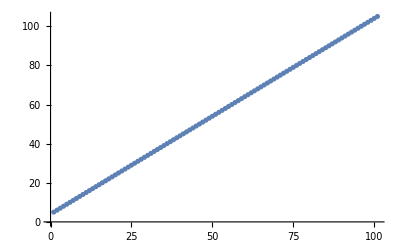

```mathematica
ListPlot[overTime]
```

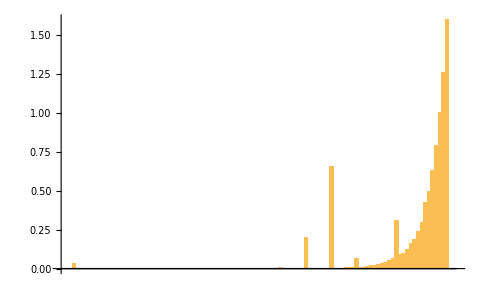

```mathematica
BarChart[run[[-1,1]]]
```

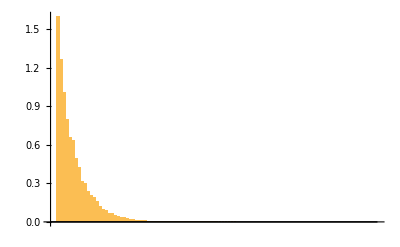

```mathematica
BarChart[ReverseSort[run[[-1,1]]]]
```